Thomas Kwok
Math 385

# Homework 5

## Problem 1

For f(x) = xe^-x - 1

a. Calculate Taylor Polynomial with x=2.5. Plot the polynomial and f on the same plot. Calculate norm error and mean norm error over interval [1,4].

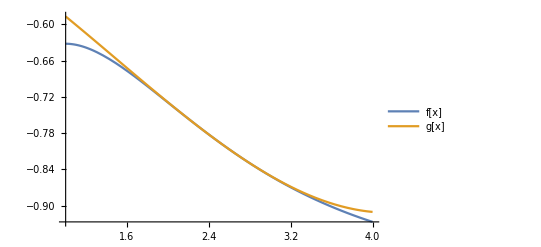

Norm Error | Mean Norm Error
0.0187681 | 0.0790952

```mathematica
f[x_]=x*E^-x-1;
a=2.5;
g[x_] = f[a] + f'[a](x-a) + (1/2!)f''[a](x-a)^2 + (1/3!)f'''[a](x-a)^3;
norm = ((f[x]-g[x])^2);
Plot[{f[x], g[x]}, {x, 1, 4}, PlotLegends-> {"f[x]", "g[x]"}]
norm = Sqrt[Integrate[norm, {x, 1, 4}]];
mnorm = 1/3 *Sqrt[ Integrate[norm, {x, 1, 4}]];
list = {{norm, mnorm}};
data = PrependTo[list, {"Norm Error", "Mean Norm Error"}];
Grid[data, Dividers->All]
```

b. Compute the Lagrange polynomial interpolation, p, of f(x) using nodes x=1,2,3,4. Plot f and p on the same axes on [1,4] and calculate the norm error and mean norm error.

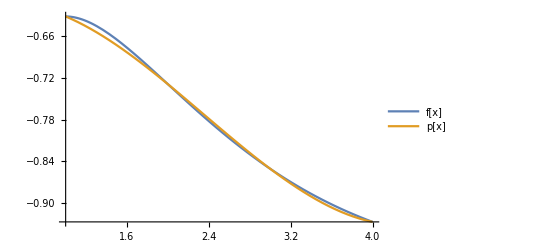

Norm Error | Mean Norm Error
0.00748051 | 0.0024935

```mathematica
f[x_]=x*E^-x-1;
l0 = ((x-2)(x-3)(x-4))/((1-2)(1-3)(1-4));
l1 = ((x-1)(x-3)(x-4))/((2-1)(2-3)(2-4));
l2 = ((x-1)(x-2)(x-4))/((3-1)(3-2)(3-4));
l3 = ((x-1)(x-2)(x-3))/((4-1)(4-2)(4-3));
P= f[1]*l0 + f[2]*l1 + f[3]*l2 + f[4]*l3;
Plot[{f[x], P}, {x, 1, 4}, PlotLegends-> {"f[x]", "p[x]"}]
norm = ((f[x]-P+0.0)^2);
normerror=Sqrt[Integrate[norm, {x, 1, 4}]];
mnorm = 1/3*Sqrt[Integrate[norm, {x, 1, 4}]];
list = {{normerror, mnorm}};
data = PrependTo[list, {"Norm Error", "Mean Norm Error"}];
Grid[data, Dividers->All]
```

c. Is p better or worst than the Taylor Interpolant?

The p is better than the Taylor Interpolant as it shows that there is a smaller Norm Error and Mean Error.

d. Use 3.1.2 to estimate the upper bound for the maximal absolute error for the Lagrange Interpolation.

|e(x)| <= (M/(n+1)!)*(b-a)^n+1 where M is maximal value of f^(n+1) on the interval

```mathematica
f[x_]=x*E^-x-1;
m= FindMaximum[{f''''[x], 1≤ x≤ 4}, x];
ex = Abs[(m[[1]]/4!)*(1)^4];
list = {{ex}};
data = PrependTo[list, {"|e(x)|"}];
Grid[data, Dividers->All]
```

|e(x)|
3.77313×10^-9

## Problem 2

Consider the function f(x) = 1/(1+x^2) on the interval [-4, 4].

a. Determine the maximal value mu = f’’’(x) on the interval.

```mathematica
f[x_]= 1/(1+x^2);
mu = FindMaximum[{f'''[x], -4≤ x≤ 4}, x];
list = {{mu[[1]]}};
data = PrependTo[list, {"mu"}];
Grid[data, Dividers->All]
```

mu
0.420964

b. Divide the interval into 40 subintervals of length 0.2. In particular determine a partition -4 = a0 < a1 < ... a40 with each ak+1 = ak+0.2

```mathematica
n=41;
p=-4;
i = 0;
list = {};
While[i≤ n, 
AppendTo[list, {i, p}];
p=p+1/5;
i++]
datalist = Table[list[[i]], {i, n}];
data = PrependTo[datalist, {"ai", "x"}];
Grid[data, Dividers-> All]
```

ai | x
0 | -4
1 | -19/5
2 | -18/5
3 | -17/5
4 | -16/5
5 | -3
6 | -14/5
7 | -13/5
8 | -12/5
9 | -11/5
10 | -2
11 | -9/5
12 | -8/5
13 | -7/5
14 | -6/5
15 | -1
16 | -4/5
17 | -3/5
18 | -2/5
19 | -1/5
20 | 0
21 | 1/5
22 | 2/5
23 | 3/5
24 | 4/5
25 | 1
26 | 6/5
27 | 7/5
28 | 8/5
29 | 9/5
30 | 2
31 | 11/5
32 | 12/5
33 | 13/5
34 | 14/5
35 | 3
36 | 16/5
37 | 17/5
38 | 18/5
39 | 19/5
40 | 4

c. Compute the second degree polynomial interpolation of f on subinterval [ak, ak+1] using the three values ak, (ak+ak+1)/2, ak+1 
k = 0, 1, 2, ... 39

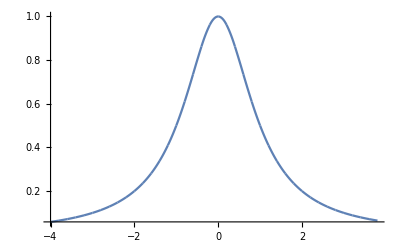

```mathematica
interval = Subdivide[-4, 4, 40];
f[x_]= 1/(1+x^2);
lagrange = {};
Do[node = {interval[[k]], (interval[[k]]+interval[[k+1]])/2, interval[[k+1]]};
l0 = ((x-node[[2]])*(x-node[[3]]))/((node[[1]]-node[[2]])*(node[[1]]-node[[3]]));
l1 = ((x-node[[1]])*(x-node[[3]]))/((node[[2]]-node[[1]])*(node[[2]]-node[[3]]));
l2 = ((x-node[[1]])*(x-node[[2]]))/((node[[3]]-node[[1]])*(node[[3]]-node[[2]]));
AppendTo[lagrange, Plot[f[node[[1]]]*l0+f[node[[2]]]*l1+f[node[[3]]]*l2,{x,interval[[k]], interval[[k+1]]}]], {k, 39}];
Show[lagrange, PlotRange -> Automatic]
```

d. Plot the result of c with the graph f(x)

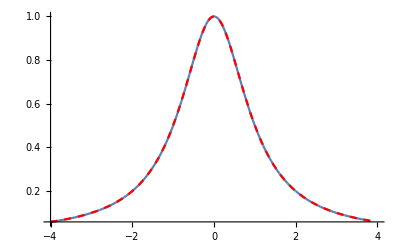

```mathematica
plotlagrange = Show[lagrange, PlotRange -> Automatic];
fplot = Plot[f[x], {x, -4, 4}, PlotStyle->{Red, Dashed}];
Show[{plotlagrange, fplot}]
```

e. Use Theorem 3.1.3 in the text to prove the absolute error |e(x)| is bounded by mu(0.2)^3/6 where mu is the value computed in Part a.

From equation 3.1.2 the absolute error |e(x)| is bounded by (M/(n+1)!)*(b-a)^(n+1). Since we are using a second degree polynomial, n = 2 and thus M = the maximum value to f^(3) derivative, which is mu from part A. Then (b-a) is 0.2 because we divided it into 40 subintervals with increments of 0.2.

```mathematica
f[x_]= 1/(1+x^2);
max = FindMaximum[{f'''[x], -4≤ x≤ 4}, x];
ex = max[[1]]/3! * (.2)^3;
list = {{ex}};
data = PrependTo[list, {"|e(x)|"}];
Grid[data, Dividers->All]
```

|e(x)|
0.000561285

## Problem 3

a. Verify that the Hermite cubics determine a Hermite interpolation on the interval [a,b].

H_(2n+1)(x) = ∑_(j=0)^n f(xj)H_(n,j)(x) + ∑_(j=0)^n f'(xi)S_(n,j)

H0(x) = 3((b-x)/(b-a))^2 - 2((b-x)/(b-a))^3 
H1(x) = 3((x-a)/(b-a))^2 - 2((x-a)/(b-a))^3
S0(x) = (b-x)^2/(b-a) - (b-x)^3/(b-a)^2  
S1(x) =   -(x-a)^2/(b-a) + (x-a)^3/((b-)

To determine a Hermite interpolation on the interval [a,b] I need to satisfy the two properties:

1. h(xi) = f(xi)
2. h’(xi) = f’(xi)

To satisfy the first property, take the points at the a and b. At x=a we have:
	H0(a) = 3((b-a)/(b-a))^2 - 2((b-a)/(b-a))^3 = 3-2=1.
	H1(a) = 3((a-a)/(b-a))^2 - 2((a-a)/(b-a))^3 = 0-0=0.
	S0(a) = (b-a)^2/(b-a) - (b-a)^3/(b-a)^2  = 1-1=0.
	S1(a) = -(a-a)^2/(b-a) + (a-a)^3/(b-a)^2 = 0-0=0.
	At x=a, H_(2n+1)(a) = ∑_(j=0)^n f(a)*1 + 0 = f(a) recalling the property that if i =/= j then Hn,j = 0.
	
At x = b we have 
	H0(b) = 3((b-b)/(b-a))^2 - 2((b-b)/(b-a))^3 = 0-0=0.
	H1(b) = 3((b-a)/(b-a))^2 - 2((b-a)/(b-a))^3 = 3-2=1.
	S0(b) = (b-b)^2/(b-a) - (b-b)^3/(b-a)^2  = 0-0=0.
	S1(b) = -(b-a)^2/(b-a) + (b-a)^3/(b-a)^2 = -1+1=0.
	At x=b, H_(2n+1)(b) = ∑_(j=0)^n f(b)*1 + 0 = f(b) recalling the property that if i =/= j then Hn,j = 0.

To satisfy the second property

```mathematica
H0[x_] = 3*((b-x)/(b-a))^2- 2*((b-x)/(b-a))^3;
H0'[x]
H1[x_] = 3*((x-a)/(b-a))^2- 2*((x-a)/(b-a))^3;
H1'[x]
S0[x_] = (b-x)^2/(b-a)-(b-x)^3/(b-a)^2;
S0'[x]
S1[x_] =- (x-a)^2/(b-a)+(x-a)^3/(b-a)^2;
S1'[x]
```

-(6 (b-x))/(-a+b)^2+(6 (b-x)^2)/(-a+b)^3

(6 (-a+x))/(-a+b)^2-(6 (-a+x)^2)/(-a+b)^3

-(2 (b-x))/(-a+b)+(3 (b-x)^2)/(-a+b)^2

-(2 (-a+x))/(-a+b)+(3 (-a+x)^2)/(-a+b)^2

H0'(x) = -(6 (b-x))/(-a+b)^2+(6 (b-x)^2)/(-a+b)^3
H1’(x) = (6 (-a+x))/(-a+b)^2-(6 (-a+x)^2)/(-a+b)^3
S0’(x) = -(2 (b-x))/(-a+b)+(3 (b-x)^2)/(-a+b)^2 
S1’(x) = -(2 (-a+x))/(-a+b)+(3 (-a+x)^2)/(-a+b)^2

At x=a we have:
	H0’(a) = -(6 (b-a))/(-a+b)^2+(6 (b-a)^2)/(-a+b)^3 = -6/(-a+b) + 6/(-a+b)= 0.
	H1’(a) = (6 (-a+a))/(-a+b)^2-(6 (-a+a)^2)/(-a+b)^3=0-0=0
	S0’(a) = -(2 (b-a))/(-a+b)+(3 (b-a)^2)/(-a+b)^2 = -2+3=1.
	S1’(a) = -(2 (-a+a))/(-a+b)+(3 (-a+a)^2)/(-a+b)^2= 0-0 = 0.
	At x=a, H_(2n+1)(a) = 0 + ∑_(j=0)^n f'(a)*1 = f’(a) recalling the property that if i =/= j then H’n,j = 0.
	
At x=b we have
	H0’(b) = -(6 (b-b))/(-a+b)^2+(6 (b-b)^2)/(-a+b)^3 = 0-0=0.
	H1’(b) = (6(-b+a))/(-a+b)^2-(6 (-b+a)^2)/(-a+b)^3= 6/(-a+b) - 6/(-a+b)= 0.
	S0’(b) = -(2 (b-b))/(-a+b)+(3 (b-b)^2)/(-a+b)^2 = 0-0=0.
	S1’(b) = -(2 (-a+b))/(-a+b)+(3 (-a+b)^2)/(-a+b)^2= -2+3=1
	At x=b, H_(2n+1)(b) = 0 + ∑_(j=0)^n f'(b)*1 = f’(b) recalling the property that if i =/= j then H’n,j = 0.

b. Repeat problem 2c but use Hermite cubics to interpolate over [ak, ak+1]

H_(2n+1)(x) = ∑_(j=0)^n f(xj)H_(n,j)(x) + ∑_(j=0)^n f'(xi)S_(n,j)

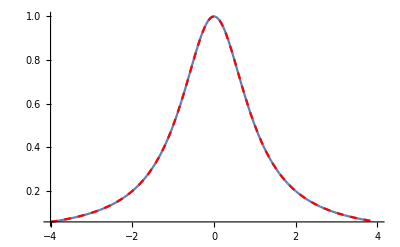

```mathematica
interval = Subdivide[-4, 4, 40];
f[x_]= 1/(1+x^2);
hermite = {};
Do[node = {interval[[k]], interval[[k+1]]};
H0[x_] = 3*((node[[2]]-x)/(node[[2]]-node[[1]]))^2- 2*((node[[2]]-x)/(node[[2]]-node[[1]]))^3;
H1[x_] = 3*((x-node[[1]])/(node[[2]]-node[[1]]))^2- 2*((x-node[[1]])/(node[[2]]-node[[1]]))^3;
S0[x_] = (node[[2]]-x)^2/(node[[2]]-node[[1]])-(node[[2]]-x)^3/(node[[2]]-node[[1]])^2;
S1[x_] =- (x-node[[1]])^2/(node[[2]]-node[[1]])+(x-node[[1]])^3/(node[[2]]-node[[1]])^2;
AppendTo[hermite, Plot[f[node[[1]]]*H0[x]+f[node[[2]]]*H1[x] + f'[node[[1]]]*S0[x]+f'[node[[2]]]*S1[x],{x,interval[[k]], interval[[k+1]]}]], {k, 39}];
hermiteplot = Show[hermite, PlotRange -> Automatic];
fplot = Plot[f[x], {x, -4, 4}, PlotStyle->{Red, Dashed}];
Show[{hermiteplot, fplot}]
```

## Problem 4

f(x) = e^(2x)- cos(2x). Use forward, backward, and central scheme to estimate derivative. Calculate error bound of each scheme and comment on best scheme

```mathematica
f[x_] = E^(2x )- Cos[2x];
list = {{-.3, -.27652,0, "N/A", "N/A" ,"N/A"}, {-.2, -.25074,0,"N/A", "N/A" ,"N/A"}, {-.1, -.16134,0,"N/A", "N/A" ,"N/A"}, {0, 0,0,"N/A", "N/A" ,"N/A"}};
For[i=0 , i <3, i++;
forward=(list[[i+1,2]]-list[[i, 2]])/(list[[i+1,1]]-list[[i,1]]);
list[[i,4]]=forward;]
	list[[4,4]] =(f[.1]-f[0])/.1;
For[i=1, i≤3, i++;
backward = (list[[i,2]]-list[[i-1, 2]])/(list[[i,1]]-list[[i-1,1]]);
list[[i, 5]] = backward];
	list[[1,5]] = (f[-.3]-f[-.4])/.1;
For[i=1, i<3, i++;
central = (list[[i+1,2]]-list[[i-1, 2]])/(list[[i+1,1]]-list[[i-1,1]]);
list[[i,6]] = central];
	list[[1,6]] = (f[-.2]-f[-.4])/.2;
	list[[4,6]] = (f[.1]-f[-.1])/.2;
For[i=0, i≤ 3, i++;
list[[i,3]] = f'[list[[i,1]]]];
data = Table[list[[i]], {i, 4}];
dataheading = PrependTo[data, {"x", "f(x)", "f'(x)", "Forward f'(x)", "Backward f'(x)", "Central f'(x)"}];
Grid[dataheading, Dividers->All]

head = {};
h=.1;
forward = FindMaximum[{f''[x], -.3≤x ≤ 0}, x];
central = FindMaximum[{f'''[x], -.3≤x≤0}, x];
forwarderror = forward[[1]]*-h/2;
backwarderror = forward[[1]]*h/2;
centralerror = -(h^2)*central[[1]]/6;
AppendTo[head, {forwarderror, backwarderror, centralerror}];
datahead = PrependTo[head, {"Forward Error Bound", "Backward Error Bound", "Central Error Bound"}];
Grid[datahead, Dividers->All]
```

x | f(x) | f'(x) | Forward f'(x) | Backward f'(x) | Central f'(x)
-0.3 | -0.27652 | -0.0316617 | 0.2578 | -0.291462 | -0.016816
-0.2 | -0.25074 | 0.561803 | 0.894 | 0.2578 | 0.5759
-0.1 | -0.16134 | 1.24012 | 1.6134 | 0.894 | 1.2537
0 | 0 | 2 | 2.41336 | 1.6134 | 2.01336

Forward Error Bound | Backward Error Bound | Central Error Bound
-0.4 | 0.4 | -0.0148461

For the data provided, I think the forward and backward schemes are better at estimating the end points whereas the central scheme is better at estimating the numbers in between. In an interval [a,b] the central scheme would fail to calculate the derivative at f(a) and f(b) as there would be no f(a-1) and f(b+1). The forward scheme would be able to calculate f(a) as it takes f(a+1)-f(a) but fail to calculate f(b) as there is no f(b+1). The backward scheme would be able to calculate f(b) but fails to calculate f(a) as there is no f(a)-f(a-1). 

From the data we were provided the central scheme did a better job at approximating the real derivative than the forward and backward scheme, but that was also because there existed f(-.4) and f(0.1) for f(x), though those fell outside of the interval [-0.3,0].

## Problem 5

Let f(x) = xe^-x-1 and set the interval to [1,4]. Consider the partition 1<1.5<2<2.5<3<3.5<4 with 6 subintervals.

a. Write a Mathematica code to compute the integral of f using trapezoid method for the given partition. Your code should work for any number of subintervals.

```mathematica
f[x_] = x*ⅇ^-x-1;
n=6;
sum = 0;
interval = N[Subdivide[1, 4, n]];
h = (interval[[n+1]]-interval[[1]])/n;
For[i=1, i< n, i++;
sum = 2*f[interval[[i]]]+sum];
sum = sum+ f[interval[[1]]] + f[interval[[n+1]]];
estimate = (h/2)*sum;
estimate
```

-2.3569

b. Use Integrate to calculate true value of integral. Calculate absolute error for your estimate in a.

```mathematica
true = N[Integrate[f[x], {x, 1, 4}]];
true
"Absolute Error"
Abs[true-estimate]
```

-2.35582

Absolute Error

0.00108001

c. Repeat part a with n=10,14,18,20 subintervals. Calculate the absolute error in each case and compare results.

```mathematica
f[x_] = x*ⅇ^-x-1;
n=10;
sum = 0;
interval = N[Subdivide[1, 4, n]];
h = (interval[[n+1]]-interval[[1]])/n;
For[i=1, i< n, i++;
sum = 2*f[interval[[i]]]+sum];
sum = sum+ f[interval[[1]]] + f[interval[[n+1]]];
estimate1 = (h/2)*sum;
estimate1;

f[x_] = x*ⅇ^-x-1;
n=14;
sum = 0;
interval = N[Subdivide[1, 4, n]];
h = (interval[[n+1]]-interval[[1]])/n;
For[i=1, i< n, i++;
sum = 2*f[interval[[i]]]+sum];
sum = sum+ f[interval[[1]]] + f[interval[[n+1]]];
estimate2 = (h/2)*sum;
estimate2;

f[x_] = x*ⅇ^-x-1;
n=18;
sum = 0;
interval = N[Subdivide[1, 4, n]];
h = (interval[[n+1]]-interval[[1]])/n;
For[i=1, i< n, i++;
sum = 2*f[interval[[i]]]+sum];
sum = sum+ f[interval[[1]]] + f[interval[[n+1]]];
estimate3 = (h/2)*sum;
estimate3;

f[x_] = x*ⅇ^-x-1;
n=20;
sum = 0;
interval = N[Subdivide[1, 4, n]];
h = (interval[[n+1]]-interval[[1]])/n;
For[i=1, i< n, i++;
sum = 2*f[interval[[i]]]+sum];
sum = sum+ f[interval[[1]]] + f[interval[[n+1]]];
estimate4= (h/2)*sum;
estimate4;

list = {{10, estimate1, true, Abs[true-estimate1]}, {14, estimate2, true, Abs[true-estimate2]}, {18, estimate3,true, Abs[true-estimate3]}, {20, estimate4, true, Abs[true-estimate4]}};
data = Table[list[[i]], {i, 4}];
dataheading = PrependTo[data, {"n", "estimate","actual integral","Absolute Error"}];
Grid[dataheading, Dividers->All]
```

n | estimate | actual integral | Absolute Error
10 | -2.35622 | -2.35582 | 0.000403653
14 | -2.35603 | -2.35582 | 0.000208052
18 | -2.35595 | -2.35582 | 0.000126385
20 | -2.35592 | -2.35582 | 0.000102496

It seems that as n increases, the absolute error decreases for the Trapezoidal method. It gets closer and closer to the actual integral. The reason for this is because when you are using the Trapezoidal method, you are trying to find the limit of the subintervals to be as close to zero as possible, which you can do by increasing n. So as n increases, the absolute error decreases and the numbers gets closer and closer to 0.

d. Estimate the upper bounds for numerical integration error in your estimates from part (a) using the bounds derived in class. Compare your bounds with your absolute errors calculated in part (c) and comment on the appropriateness of the bounds.

```mathematica
f[x_] = x*ⅇ^-x-1;
n=6;
sum = 0;
interval = N[Subdivide[1, 4, n]];
h = (interval[[n+1]]-interval[[1]])/n;
For[i=1, i< n, i++;
sum = 2*f[interval[[i]]]+sum];
sum = sum+ f[interval[[1]]] + f[interval[[n+1]]];
estimate = (h/2)*sum;
max = FindMaximum[{f''[x], 1≤x≤4}, x];
"Upper Bound"
bound = h^3*max[[1]]/12
```

Upper Bound

0.000518615

Comparing the upper bound for the numerical integration to the absolute errors I calculated from part c, it seems that the bound is appropriate as it is above all of the absolute errors in part c so it is a true upper bound.